```mathematica
TripleFromFigure[fig_]:={(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,2])/4,Mod[(#-Mod[#,2])/2,2],Mod[#,2]}&[fig];
FigureFromTriple[{σ_,κ_,δ_}]:=4σ + 2 κ + δ;MyInstructionsTable[S_,nb_]:=Thread[Flatten[Table[{i,j},{i,S-1,0,-1},{j,1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,2])/4,Mod[(#-Mod[#,2])/2,2],Mod[#,2]}&/@PadLeft[IntegerDigits[nb,4S],2S ])];MTNumberFromTriples[S_,mytriplets_]:=FromDigits[Thread[FigureFromTriple[#]&[mytriplets]],4S ];
ChangeNumbering[S_,number_]:=FromDigits[Flatten[Reverse[Partition[PadLeft[IntegerDigits[number,4S ],2S ],2]]],4S ];
SBTM[S_,nb_,limit_]:=Module[{tm},{tm=TuringMachine[{ChangeNumbering[S,nb],S,2},{{1,0},{{},0}},limit];
step=If[MemberQ[Transpose[Transpose[tm][[1]]][[3]],1],First[Position[Transpose[Transpose[tm][[1]]][[3]],1]][[1]],limit]-1;Clear[tm];tm=TuringMachine[{ChangeNumbering[S,nb],S,2},{{1,0},{{},0}},step];
delta=If[1-Min[Transpose[Transpose[tm][[1]]][[3]]]>0,1-Min[Transpose[Transpose[tm][[1]]][[3]]],0];
tm12=Transpose[Transpose[tm][[1]]][[2]];tm11=Transpose[Transpose[tm][[1]]][[1]];f[nb]=ArrayPlot[Last/@tm,Mesh->True,PlotLabel->{S,nb},LabelStyle->Directive[Bold],Epilog->{{Red,Thick,Line[{{delta,0},{delta,step+1}}]},Orange,Thickness[0.15/(step+1)],Arrowheads[0.5/(step+1)],Table[Rotate[Arrow[{{-1/2+tm12[[i]],2/10+1+step-i},{-1/2+tm12[[i]],4/5+1+step-i}}],-2π/S(tm11[[i]]-1)],{i,step+1}]}]};f[nb]];
activetriples[S_,nb_]:=MyInstructionsTable[S,nb][[All,2]];
Base4SEvolution[S_,nb_,limit_]:=Module[{a,sigma=0,activatedtriple},i=0;a[_]=0;n=ninf=-1;sigma=0;figures={};res={{1,0,-1,{0}}};While[n<0 && i<limit,{activatedtriple=activetriples[S,nb][[2S-2sigma-a[n]]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]]};figures=AppendTo[figures,FigureFromTriple[activatedtriple]];res=AppendTo[res,{i+2,sigma,n,Table[a[j],{j,ninf,n}]}];i++];figures];
Base4SPositions[S_,nb_,limit_]:=Module[{a,sigma=0,activatedtriple},i=0;a[_]=0;n=ninf=-1;sigma=0;indices={};res={{1,0,-1,{0}}};While[n<0 && i<limit,{activatedtriple=activetriples[S,nb][[2S-2sigma-a[n]]];indices=AppendTo[indices,2S-2sigma-a[n]];a[n]=activatedtriple[[2]];n=n-1+2activatedtriple[[3]];ninf=Min[n,ninf];sigma=activatedtriple[[1]]};res=AppendTo[res,{i+2,sigma,n,Table[a[j],{j,ninf,n}]}];i++];indices];
SingleTMStep[rule_, {S_, tape_, pos_} /; pos>Length[tape]] := SingleTMStep[rule,{S, Prepend[tape,0], pos}]
SingleTMStep[rule_, {S_, tape_, pos_}] := Apply[{#1,ReplacePart[tape,#2,-pos],pos-#3}&,Replace[{S,tape[[-pos]]},rule]]
SingleTMEvolve[rule_, tape_, bound_] := NestWhile[SingleTMStep[rule, #]&, {1,tape,1}, ( 18>#[[3]]>0)&,1,bound]  (*  à adapter !!!  *)
SingleTMEvolveList[rule_, tape_, bound_] := NestWhileList[SingleTMStep[rule, #]&, {1,tape,1},( 18>#[[3]]>0)&,1,bound]   (*  à adapter !!!  *)
WolframInstructionsTable[S_,nb_]:=Reverse[Thread[Flatten[Table[{i+1,j},{i,S-1,0,-1},{j,1,0,-1}],1]->({(#-Mod[#,2]-2Mod[(#-Mod[#,2])/2,2])/4+1,Mod[(#-Mod[#,2])/2,2],2Mod[#,2]-1}&/@PadLeft[IntegerDigits[nb,4S ],2S ])]]
rules[S_]:=Table[Thread[Thread[Partition[Flatten[Permutations[Partition[Range[4S-1,4,-1],4]]],4S-4]->Table[Range[4S-1,4,-1],{(S-1)!}]][[k]]],{k,(S-1)!}];symS[nb_,S_]:=Module[{},{u=Partition[PadLeft[IntegerDigits[nb,4S],2S],2]};FromDigits[#,4S]&/@MapThread[ReplaceAll,{Partition[Flatten[    Map[Append[#,Last[u]]&,   (Permute[    Most[u],#]& /@Permutations[Range[S-1]])      ]],2S],rules[S]  }]]
```

```mathematica
equivalents[S_,v_,pos_]:=Flatten[Table[Evaluate@ReplacePart[v,Thread[pos->Table[i[k],{k,Length[pos]}]]],Evaluate[Sequence@@Map[{#,0,4S-1}&,Table[i[k],{k,Length[pos]}]]]],2]
```

```mathematica
(*Ce pgm construit une table à partir d'une liste, v, où les éléments en positions donnés par pos vont de 0 à n (ici 2, ici par pas de 1)*)
Clear[i,k];v={5,4,0,6};
pos={1,3};
vars=Table[ii[k],{k,Length[pos]}];
Flatten[Table[Evaluate@ReplacePart[v,Thread[pos->vars]],Evaluate[Sequence@@Map[{#,0,2,1}&,vars]]],1]
```

{{0,4,0,6},{0,4,1,6},{0,4,2,6},{1,4,0,6},{1,4,1,6},{1,4,2,6},{2,4,0,6},{2,4,1,6},{2,4,2,6}}

```mathematica
vars
```

{i[1],i[2]}

```mathematica
ReplacePart[v,Thread[pos->vars]]
```

{i[1],4,i[2],6}

```mathematica
debutclones[S_,nb_]:=FromDigits[#,4  S]&/@    Partition[Flatten[Table[Evaluate@ReplacePart[v=PadLeft[IntegerDigits[nb,4S ],2S ],Thread[Complement[Range[2S],Union[Base4SPositions[S,nb,50]]]->Table[ii[k],{k,Length[Complement[Range[2S],Union[Base4SPositions[S,nb,50]]]]}]]],Evaluate[Sequence@@Map[{#,0,4S-1}&,Table[ii[k],{k,Length[Complement[Range[2S],Union[Base4SPositions[S,nb,50]]]]}]]]]][[1;;100]] ,2S]
```

```mathematica
debutclones[2,4]
```

{4,12,20,28,36,44,52,60,516,524,532,540,548,556,564,572,1028,1036,1044,1052,1060,1068,1076,1084,1540}

```mathematica
Table[{k,Base4SPositions[2,k,50]},{k,0,7,2}]
```

{{0,{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}},{2,{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}},{4,{4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2}},{6,{4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2,4,2}}}

```mathematica
FindSequenceFunction[clones[2,0]]
```

8 (-1+#1)&

```mathematica
FindSequenceFunction[clones[2,2]]
```

2 (-3+4 #1)&

```mathematica
clones[2,4]
```

{4,12,20,28,36,44,52,60,516,524,532,540,548,556,564,572,1028,1036,1044,1052,1060,1068,1076,1084,1540,1548,1556,1564,1572,1580,1588,1596,2052,2060,2068,2076,2084,2092,2100,2108,2564,2572,2580,2588,2596,2604,2612,2620,3076,3084,3092,3100,3108,3116,3124,3132,3588,3596,3604,3612,3620,3628,3636,3644}

```mathematica
Sort[Flatten[Table[8^3 k+8^2 j+8^1 l+0,{j,0,7},{k,0,7},{l,0,7}]]]==clones[2,0]
```

True

```mathematica
Sort[Flatten[Table[8^3 k+8^2 j+8^1 l+2,{j,0,7},{k,0,7},{l,0,7}]]]==clones[2,2]
```

True

```mathematica
Sort[Flatten[Table[8^3 k+8^1 j+4,{j,0,7},{k,0,7}]]]==clones[2,4]
```

True

```mathematica
Sort[Flatten[Table[8^3 k+8^1 j+6,{j,0,7},{k,0,7}]]]==clones[2,6]
```

True

```mathematica
Table[{k,Base4SPositions[3,k,50]},{k,0,11,2}]
```

{{0,{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}},{2,{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}},{4,{6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4}},{6,{6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4,6,4}},{8,{6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2}},{10,{6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2}}}

```mathematica
Sort[Flatten[Table[12^5 i+12^4 l+12^3 k+12^2 m+12^1 j+0,{i,0,11},{l,0,11},{j,0,11},{k,0,11},{m,0,11}]]]==clones[3,0]
```

True

```mathematica
Sort[Flatten[Table[12^5 i+12^4 l+12^3 k+12^2 m+12^1 j+2,{i,0,11},{l,0,11},{j,0,11},{k,0,11},{m,0,11}]]]==clones[3,2]
```

True

```mathematica
Sort[Flatten[Table[12^5 i+12^4 l+12^3 k+12^1 j+4,{i,0,11},{l,0,11},{j,0,11},{k,0,11}]]]==clones[3,4]
```

True

```mathematica
Sort[Flatten[Table[12^5 i+12^4 l+12^3 k+12^1 j+6,{i,0,11},{l,0,11},{j,0,11},{k,0,11}]]]==clones[3,6]
```

True

```mathematica
Sort[Flatten[Table[12^5 i+12^3 l+12^2 k+12^1 j+8,{i,0,11},{l,0,11},{j,0,11},{k,0,11}]]]==clones[3,8]
```

True

```mathematica
Sort[Flatten[Table[12^5 i+12^3 l+12^2 k+12^1 j+10,{i,0,11},{l,0,11},{j,0,11},{k,0,11}]]]==clones[3,10]
```

True

```mathematica
Table[{k,Base4SPositions[3,k,50]},{k,1000,1011,2}]
```

{{1000,{6,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}},{1002,{6,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}},{1004,{6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2}},{1006,{6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2,6,2}},{1008,{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}},{1010,{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}}}

```mathematica
12 12 12
```

1728

```mathematica
(2596-868)/(12 12 12)
```

1

```mathematica
Sort[Flatten[Table[12^5 i+12^4 l+12^3 k+12^1 j+868,{i,0,11},{j,0,11},{k,0,11},{l,0,11}]]]==clones[3,868]
```

True

```mathematica
MemberQ[clones[3,4],868]
```

False

```mathematica
Sort[Flatten[Table[12^5 i+12^4 l+12^3 k+12^1 j+868,{i,0,11},{j,0,11},{k,0,11},{l,0,11}]]]
```

{868,880,892,904,916,928,940,952,964,976,988,1000,2596,2608,2620,2632,2644,2656,2668,2680,2692,2704,2716,2728,4324,4336,4348,4360,4372,4384,4396,4408,4420,4432,4444,4456,6052,6064,6076,6088,6100,6112,6124,6136,6148,6160,6172,6184,7780,7792,7804,7816,7828,7840,7852,7864,7876,7888,7900,7912,9508,9520,9532,9544,9556,9568,9580,9592,9604,9616,9628,9640,11236,11248,11260,11272,11284,11296,11308,11320,11332,11344,11356,11368,12964,12976,12988,13000,13012,13024,13036,13048,13060,13072,13084,13096,14692,14704,14716,14728,14740,14752,14764,14776,14788,14800,14812,14824,16420,16432,16444,16456,16468,16480,16492,16504,16516,16528,16540,16552,18148,18160,18172,18184,18196,18208,18220,18232,18244,18256,18268,18280,19876,19888,19900,19912,19924,19936,19948,19960,19972,19984,19996,20008,249700,249712,249724,249736,249748,249760,249772,249784,249796,249808,249820,249832,251428,251440,251452,251464,251476,251488,251500,251512,251524,251536,251548,251560,253156,253168,253180,253192,253204,253216,253228,253240,253252,253264,253276,253288,254884,254896,254908,254920,254932,254944,254956,254968,254980,254992,255004,255016,256612,256624,256636,256648,256660,256672,256684,256696,256708,256720,256732,256744,258340,258352,258364,258376,258388,258400,258412,258424,258436,258448,258460,258472,260068,260080,260092,260104,260116,260128,260140,260152,260164,260176,260188,260200,261796,261808,261820,261832,261844,261856,261868,261880,261892,261904,261916,261928,263524,263536,263548,263560,263572,263584,263596,263608,263620,263632,263644,263656,265252,265264,265276,265288,265300,265312,265324,265336,265348,265360,265372,265384,266980,266992,267004,267016,267028,267040,267052,267064,267076,267088,267100,267112,268708,268720,268732,268744,268756,268768,268780,268792,268804,268816,268828,268840,498532,498544,498556,498568,498580,498592,498604,498616,498628,498640,498652,498664,500260,500272,500284,500296,500308,500320,500332,500344,500356,500368,500380,500392,501988,502000,502012,502024,502036,502048,502060,502072,502084,502096,502108,502120,503716,503728,503740,503752,503764,503776,503788,503800,503812,503824,503836,503848,505444,505456,505468,505480,505492,505504,505516,505528,505540,505552,505564,505576,507172,507184,507196,507208,507220,507232,507244,507256,507268,507280,507292,507304,508900,508912,508924,508936,508948,508960,508972,508984,508996,509008,509020,509032,510628,510640,510652,510664,510676,510688,510700,510712,510724,510736,510748,510760,512356,512368,512380,512392,512404,512416,512428,512440,512452,512464,512476,512488,514084,514096,514108,514120,514132,514144,514156,514168,514180,514192,514204,514216,515812,515824,515836,515848,515860,515872,515884,515896,515908,515920,515932,515944,517540,517552,517564,517576,517588,517600,517612,517624,517636,517648,517660,517672,747364,747376,747388,747400,747412,747424,747436,747448,747460,747472,747484,747496,749092,749104,749116,749128,749140,749152,749164,749176,749188,749200,749212,749224,750820,750832,750844,750856,750868,750880,750892,750904,750916,750928,750940,750952,752548,752560,752572,752584,752596,752608,752620,752632,752644,752656,752668,752680,754276,754288,754300,754312,754324,754336,754348,754360,754372,754384,754396,754408,756004,756016,756028,756040,756052,756064,756076,756088,756100,756112,756124,756136,757732,757744,757756,757768,757780,757792,757804,757816,757828,757840,757852,757864,759460,759472,759484,759496,759508,759520,759532,759544,759556,759568,759580,759592,761188,761200,761212,761224,761236,761248,761260,761272,761284,761296,761308,761320,762916,762928,762940,762952,762964,762976,762988,763000,763012,763024,763036,763048,764644,764656,764668,764680,764692,764704,764716,764728,764740,764752,764764,764776,766372,766384,766396,766408,766420,766432,766444,766456,766468,766480,766492,766504,996196,996208,996220,996232,996244,996256,996268,996280,996292,996304,996316,996328,997924,997936,997948,997960,997972,997984,997996,998008,998020,998032,998044,998056,999652,999664,999676,999688,999700,999712,999724,999736,999748,999760,999772,999784,1001380,1001392,1001404,1001416,1001428,1001440,1001452,1001464,1001476,1001488,1001500,1001512,1003108,1003120,1003132,1003144,1003156,1003168,1003180,1003192,1003204,1003216,1003228,1003240,1004836,1004848,1004860,1004872,1004884,1004896,1004908,1004920,1004932,1004944,1004956,1004968,1006564,1006576,1006588,1006600,1006612,1006624,1006636,1006648,1006660,1006672,1006684,1006696,1008292,1008304,1008316,1008328,1008340,1008352,1008364,1008376,1008388,1008400,1008412,1008424,1010020,1010032,1010044,1010056,1010068,1010080,1010092,1010104,1010116,1010128,1010140,1010152,1011748,1011760,1011772,1011784,1011796,1011808,1011820,1011832,1011844,1011856,1011868,1011880,1013476,1013488,1013500,1013512,1013524,1013536,1013548,1013560,1013572,1013584,1013596,1013608,1015204,1015216,1015228,1015240,1015252,1015264,1015276,1015288,1015300,1015312,1015324,1015336,1245028,1245040,1245052,1245064,1245076,1245088,1245100,1245112,1245124,1245136,1245148,1245160,1246756,1246768,1246780,1246792,1246804,1246816,1246828,1246840,1246852,1246864,1246876,1246888,1248484,1248496,1248508,1248520,1248532,1248544,1248556,1248568,1248580,1248592,1248604,1248616,1250212,1250224,1250236,1250248,1250260,1250272,1250284,1250296,1250308,1250320,1250332,1250344,1251940,1251952,1251964,1251976,1251988,1252000,1252012,1252024,1252036,1252048,1252060,1252072,1253668,1253680,1253692,1253704,1253716,1253728,1253740,1253752,1253764,1253776,1253788,1253800,1255396,1255408,1255420,1255432,1255444,1255456,1255468,1255480,1255492,1255504,1255516,1255528,1257124,1257136,1257148,1257160,1257172,1257184,1257196,1257208,1257220,1257232,1257244,1257256,1258852,1258864,1258876,1258888,1258900,1258912,1258924,1258936,1258948,1258960,1258972,1258984,1260580,1260592,1260604,1260616,1260628,1260640,1260652,1260664,1260676,1260688,1260700,1260712,1262308,1262320,1262332,1262344,1262356,1262368,1262380,1262392,1262404,1262416,1262428,1262440,1264036,1264048,1264060,1264072,1264084,1264096,1264108,1264120,1264132,1264144,1264156,1264168,1493860,1493872,1493884,1493896,1493908,1493920,1493932,1493944,1493956,1493968,1493980,1493992,1495588,1495600,1495612,1495624,1495636,1495648,1495660,1495672,1495684,1495696,1495708,1495720,1497316,1497328,1497340,1497352,1497364,1497376,1497388,1497400,1497412,1497424,1497436,1497448,1499044,1499056,1499068,1499080,1499092,1499104,1499116,1499128,1499140,1499152,1499164,1499176,1500772,1500784,1500796,1500808,1500820,1500832,1500844,1500856,1500868,1500880,1500892,1500904,1502500,1502512,1502524,1502536,1502548,1502560,1502572,1502584,1502596,1502608,1502620,1502632,1504228,1504240,1504252,1504264,1504276,1504288,1504300,1504312,1504324,1504336,1504348,1504360,1505956,1505968,1505980,1505992,1506004,1506016,1506028,1506040,1506052,1506064,1506076,1506088,1507684,1507696,1507708,1507720,1507732,1507744,1507756,1507768,1507780,1507792,1507804,1507816,1509412,1509424,1509436,1509448,1509460,1509472,1509484,1509496,1509508,1509520,1509532,1509544,1511140,1511152,1511164,1511176,1511188,1511200,1511212,1511224,1511236,1511248,1511260,1511272,1512868,1512880,1512892,1512904,1512916,1512928,1512940,1512952,1512964,1512976,1512988,1513000,1742692,1742704,1742716,1742728,1742740,1742752,1742764,1742776,1742788,1742800,1742812,1742824,1744420,1744432,1744444,1744456,1744468,1744480,1744492,1744504,1744516,1744528,1744540,1744552,1746148,1746160,1746172,1746184,1746196,1746208,1746220,1746232,1746244,1746256,1746268,1746280,1747876,1747888,1747900,1747912,1747924,1747936,1747948,1747960,1747972,1747984,1747996,1748008,1749604,1749616,1749628,1749640,1749652,1749664,1749676,1749688,1749700,1749712,1749724,1749736,1751332,1751344,1751356,1751368,1751380,1751392,1751404,1751416,1751428,1751440,1751452,1751464,1753060,1753072,1753084,1753096,1753108,1753120,1753132,1753144,1753156,1753168,1753180,1753192,1754788,1754800,1754812,1754824,1754836,1754848,1754860,1754872,1754884,1754896,1754908,1754920,1756516,1756528,1756540,1756552,1756564,1756576,1756588,1756600,1756612,1756624,1756636,1756648,1758244,1758256,1758268,1758280,1758292,1758304,1758316,1758328,1758340,1758352,1758364,1758376,1759972,1759984,1759996,1760008,1760020,1760032,1760044,1760056,1760068,1760080,1760092,1760104,1761700,1761712,1761724,1761736,1761748,1761760,1761772,1761784,1761796,1761808,1761820,1761832,1991524,1991536,1991548,1991560,1991572,1991584,1991596,1991608,1991620,1991632,1991644,1991656,1993252,1993264,1993276,1993288,1993300,1993312,1993324,1993336,1993348,1993360,1993372,1993384,1994980,1994992,1995004,1995016,1995028,1995040,1995052,1995064,1995076,1995088,1995100,1995112,1996708,1996720,1996732,1996744,1996756,1996768,1996780,1996792,1996804,1996816,1996828,1996840,1998436,1998448,1998460,1998472,1998484,1998496,1998508,1998520,1998532,1998544,1998556,1998568,2000164,2000176,2000188,2000200,2000212,2000224,2000236,2000248,2000260,2000272,2000284,2000296,2001892,2001904,2001916,2001928,2001940,2001952,2001964,2001976,2001988,2002000,2002012,2002024,2003620,2003632,2003644,2003656,2003668,2003680,2003692,2003704,2003716,2003728,2003740,2003752,2005348,2005360,2005372,2005384,2005396,2005408,2005420,2005432,2005444,2005456,2005468,2005480,2007076,2007088,2007100,2007112,2007124,2007136,2007148,2007160,2007172,2007184,2007196,2007208,2008804,2008816,2008828,2008840,2008852,2008864,2008876,2008888,2008900,2008912,2008924,2008936,2010532,2010544,2010556,2010568,2010580,2010592,2010604,2010616,2010628,2010640,2010652,2010664,2240356,2240368,2240380,2240392,2240404,2240416,2240428,2240440,2240452,2240464,2240476,2240488,2242084,2242096,2242108,2242120,2242132,2242144,2242156,2242168,2242180,2242192,2242204,2242216,2243812,2243824,2243836,2243848,2243860,2243872,2243884,2243896,2243908,2243920,2243932,2243944,2245540,2245552,2245564,2245576,2245588,2245600,2245612,2245624,2245636,2245648,2245660,2245672,2247268,2247280,2247292,2247304,2247316,2247328,2247340,2247352,2247364,2247376,2247388,2247400,2248996,2249008,2249020,2249032,2249044,2249056,2249068,2249080,2249092,2249104,2249116,2249128,2250724,2250736,2250748,2250760,2250772,2250784,2250796,2250808,2250820,2250832,2250844,2250856,2252452,2252464,2252476,2252488,2252500,2252512,2252524,2252536,2252548,2252560,2252572,2252584,2254180,2254192,2254204,2254216,2254228,2254240,2254252,2254264,2254276,2254288,2254300,2254312,2255908,2255920,2255932,2255944,2255956,2255968,2255980,2255992,2256004,2256016,2256028,2256040,2257636,2257648,2257660,2257672,2257684,2257696,2257708,2257720,2257732,2257744,2257756,2257768,2259364,2259376,2259388,2259400,2259412,2259424,2259436,2259448,2259460,2259472,2259484,2259496,2489188,2489200,2489212,2489224,2489236,2489248,2489260,2489272,2489284,2489296,2489308,2489320,2490916,2490928,2490940,2490952,2490964,2490976,2490988,2491000,2491012,2491024,2491036,2491048,2492644,2492656,2492668,2492680,2492692,2492704,2492716,2492728,2492740,2492752,2492764,2492776,2494372,2494384,2494396,2494408,2494420,2494432,2494444,2494456,2494468,2494480,2494492,2494504,2496100,2496112,2496124,2496136,2496148,2496160,2496172,2496184,2496196,2496208,2496220,2496232,2497828,2497840,2497852,2497864,2497876,2497888,2497900,2497912,2497924,2497936,2497948,2497960,2499556,2499568,2499580,2499592,2499604,2499616,2499628,2499640,2499652,2499664,2499676,2499688,2501284,2501296,2501308,2501320,2501332,2501344,2501356,2501368,2501380,2501392,2501404,2501416,2503012,2503024,2503036,2503048,2503060,2503072,2503084,2503096,2503108,2503120,2503132,2503144,2504740,2504752,2504764,2504776,2504788,2504800,2504812,2504824,2504836,2504848,2504860,2504872,2506468,2506480,2506492,2506504,2506516,2506528,2506540,2506552,2506564,2506576,2506588,2506600,2508196,2508208,2508220,2508232,2508244,2508256,2508268,2508280,2508292,2508304,2508316,2508328,2738020,2738032,2738044,2738056,2738068,2738080,2738092,2738104,2738116,2738128,2738140,2738152,2739748,2739760,2739772,2739784,2739796,2739808,2739820,2739832,2739844,2739856,2739868,2739880,2741476,2741488,2741500,2741512,2741524,2741536,2741548,2741560,2741572,2741584,2741596,2741608,2743204,2743216,2743228,2743240,2743252,2743264,2743276,2743288,2743300,2743312,2743324,2743336,2744932,2744944,2744956,2744968,2744980,2744992,2745004,2745016,2745028,2745040,2745052,2745064,2746660,2746672,2746684,2746696,2746708,2746720,2746732,2746744,2746756,2746768,2746780,2746792,2748388,2748400,2748412,2748424,2748436,2748448,2748460,2748472,2748484,2748496,2748508,2748520,2750116,2750128,2750140,2750152,2750164,2750176,2750188,2750200,2750212,2750224,2750236,2750248,2751844,2751856,2751868,2751880,2751892,2751904,2751916,2751928,2751940,2751952,2751964,2751976,2753572,2753584,2753596,2753608,2753620,2753632,2753644,2753656,2753668,2753680,2753692,2753704,2755300,2755312,2755324,2755336,2755348,2755360,2755372,2755384,2755396,2755408,2755420,2755432,2757028,2757040,2757052,2757064,2757076,2757088,2757100,2757112,2757124,2757136,2757148,2757160}

```mathematica
clones[3,868]
```

```mathematica
2985256-868
```

2984388

```mathematica
12^6
```

2985984

```mathematica
Length[clones[3,4]]
```

20736

```mathematica
Table[{k,Base4SPositions[4,k,50]},{k,0,15,2}]
```

{{0,{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}},{2,{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}},{4,{8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6}},{6,{8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6,8,6}},{8,{8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4}},{10,{8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4}},{12,{8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2}},{14,{8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2,8,2}}}

```mathematica
Table[{k,Base4SPositions[5,k,50]},{k,0,19,2}]
```

{{0,{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}},{2,{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}},{4,{10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8}},{6,{10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8,10,8}},{8,{10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6}},{10,{10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6,10,6}},{12,{10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4}},{14,{10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4,10,4}},{16,{10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2}},{18,{10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2}}}

```mathematica
Base4SPositions[5,20+18,50]
```

{10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2,10,2}

```mathematica
Table[FindSequenceFunction[clones[k,0][[1;;100]]],{k,2,4}]
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

SystemException[MemoryAllocationFailure,{Table[FindSequenceFunction[clones[k,0]⟦1;;100⟧],{k,2,4}],FindSequenceFunction[clones[k,0]⟦1;;100⟧],clones[k,0]⟦1;;100⟧,(FromDigits[#1,4 4]&)/@Partition[Flatten[Table[Evaluate[ReplacePart[v=PadLeft[IntegerDigits[0,4 4],2 4],Thread[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]→Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],Evaluate[Sequence@@({#1,0,4 4-1}&)/@Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],2 4],Partition[Flatten[Table[Evaluate[ReplacePart[v=PadLeft[IntegerDigits[0,4 4],2 4],Thread[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]→Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],Evaluate[Sequence@@({#1,0,4 4-1}&)/@Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],2 4],Flatten[Table[Evaluate[ReplacePart[v=PadLeft[IntegerDigits[0,4 4],2 4],Thread[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]→Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],Evaluate[Sequence@@({#1,0,4 4-1}&)/@Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],Table[{ii[1],ii[2],ii[3],ii[4],ii[5],ii[6],ii[7],0},{ii[1],0,15},{ii[2],0,15},{ii[3],0,15},{ii[4],0,15},{ii[5],0,15},{ii[6],0,15},{ii[7],0,15}]}]

```mathematica
12^6
```

2985984

```mathematica
clones[S_,nb_]:=FromDigits[#,4  S]&/@    Partition[Flatten[Table[Evaluate@ReplacePart[v=PadLeft[IntegerDigits[nb,4S ],2S ],Thread[Complement[Range[2S],Union[Base4SPositions[S,nb,50]]]->Table[ii[k],{k,Length[Complement[Range[2S],Union[Base4SPositions[S,nb,50]]]]}]]],Evaluate[Sequence@@Map[{#,0,4S-1}&,Table[ii[k],{k,Length[Complement[Range[2S],Union[Base4SPositions[S,nb,50]]]]}]]]]] ,2S]
```

```mathematica
clones[2,0]
```

{0,8,16,24,32,40,48,56,64,72,80,88,96,104,112,120,128,136,144,152,160,168,176,184,192,200,208,216,224,232,240,248,256,264,272,280,288,296,304,312,320,328,336,344,352,360,368,376,384,392,400,408,416,424,432,440,448,456,464,472,480,488,496,504,512,520,528,536,544,552,560,568,576,584,592,600,608,616,624,632,640,648,656,664,672,680,688,696,704,712,720,728,736,744,752,760,768,776,784,792,800,808,816,824,832,840,848,856,864,872,880,888,896,904,912,920,928,936,944,952,960,968,976,984,992,1000,1008,1016,1024,1032,1040,1048,1056,1064,1072,1080,1088,1096,1104,1112,1120,1128,1136,1144,1152,1160,1168,1176,1184,1192,1200,1208,1216,1224,1232,1240,1248,1256,1264,1272,1280,1288,1296,1304,1312,1320,1328,1336,1344,1352,1360,1368,1376,1384,1392,1400,1408,1416,1424,1432,1440,1448,1456,1464,1472,1480,1488,1496,1504,1512,1520,1528,1536,1544,1552,1560,1568,1576,1584,1592,1600,1608,1616,1624,1632,1640,1648,1656,1664,1672,1680,1688,1696,1704,1712,1720,1728,1736,1744,1752,1760,1768,1776,1784,1792,1800,1808,1816,1824,1832,1840,1848,1856,1864,1872,1880,1888,1896,1904,1912,1920,1928,1936,1944,1952,1960,1968,1976,1984,1992,2000,2008,2016,2024,2032,2040,2048,2056,2064,2072,2080,2088,2096,2104,2112,2120,2128,2136,2144,2152,2160,2168,2176,2184,2192,2200,2208,2216,2224,2232,2240,2248,2256,2264,2272,2280,2288,2296,2304,2312,2320,2328,2336,2344,2352,2360,2368,2376,2384,2392,2400,2408,2416,2424,2432,2440,2448,2456,2464,2472,2480,2488,2496,2504,2512,2520,2528,2536,2544,2552,2560,2568,2576,2584,2592,2600,2608,2616,2624,2632,2640,2648,2656,2664,2672,2680,2688,2696,2704,2712,2720,2728,2736,2744,2752,2760,2768,2776,2784,2792,2800,2808,2816,2824,2832,2840,2848,2856,2864,2872,2880,2888,2896,2904,2912,2920,2928,2936,2944,2952,2960,2968,2976,2984,2992,3000,3008,3016,3024,3032,3040,3048,3056,3064,3072,3080,3088,3096,3104,3112,3120,3128,3136,3144,3152,3160,3168,3176,3184,3192,3200,3208,3216,3224,3232,3240,3248,3256,3264,3272,3280,3288,3296,3304,3312,3320,3328,3336,3344,3352,3360,3368,3376,3384,3392,3400,3408,3416,3424,3432,3440,3448,3456,3464,3472,3480,3488,3496,3504,3512,3520,3528,3536,3544,3552,3560,3568,3576,3584,3592,3600,3608,3616,3624,3632,3640,3648,3656,3664,3672,3680,3688,3696,3704,3712,3720,3728,3736,3744,3752,3760,3768,3776,3784,3792,3800,3808,3816,3824,3832,3840,3848,3856,3864,3872,3880,3888,3896,3904,3912,3920,3928,3936,3944,3952,3960,3968,3976,3984,3992,4000,4008,4016,4024,4032,4040,4048,4056,4064,4072,4080,4088}

```mathematica
Length[clones[4,0]]
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

SystemException[MemoryAllocationFailure,{Length[clones[4,0]],(FromDigits[#1,4 4]&)/@Partition[Flatten[Table[Evaluate[ReplacePart[v=PadLeft[IntegerDigits[0,4 4],2 4],Thread[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]→Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],Evaluate[Sequence@@({#1,0,4 4-1}&)/@Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],2 4],Partition[Flatten[Table[Evaluate[ReplacePart[v=PadLeft[IntegerDigits[0,4 4],2 4],Thread[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]→Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],Evaluate[Sequence@@({#1,0,4 4-1}&)/@Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],2 4],Flatten[Table[Evaluate[ReplacePart[v=PadLeft[IntegerDigits[0,4 4],2 4],Thread[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]→Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],Evaluate[Sequence@@({#1,0,4 4-1}&)/@Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],Table[{ii[1],ii[2],ii[3],ii[4],ii[5],ii[6],ii[7],0},{ii[1],0,15},{ii[2],0,15},{ii[3],0,15},{ii[4],0,15},{ii[5],0,15},{ii[6],0,15},{ii[7],0,15}]}]

```mathematica
x=10;While[x>0,x=Floor[x/2]];x
```

```mathematica
4294967296/2
```

2147483648

```mathematica
Table[(4S)^(2S),{S,2,5}]
```

{4096,2985984,4294967296,10240000000000}

```mathematica
cpt=0;result={};Clear[F];F[x_Integer]:=1;   (*S=2*)
```

```mathematica
Timing[While[cpt<4096,{result=Append[result,{cpt,Length[clones[2,cpt]]}];Map[(F[#]=0)&,clones[2,cpt]];While[F[cpt]==0,cpt=cpt+2];}]]
```

{1.139,Null}

```mathematica
(8 s^2-10s-7)(4s)^(2s-2)/.s->5
```

3660800000000

```mathematica
2048-1024-11*64
```

320

```mathematica
result
```

{{0,512},{2,512},{4,64},{6,64},{68,64},{70,8},{78,8},{86,8},{94,8},{102,8},{110,8},{118,8},{126,8},{132,64},{134,64},{196,8},{198,8},{206,8},{214,8},{222,8},{230,1},{238,8},{246,1},{254,8},{260,64},{262,64},{324,64},{326,8},{388,64},{390,64},{452,64},{454,1},{462,1},{470,1},{478,1},{486,1},{494,1},{502,1},{510,1},{708,8},{742,1},{758,1},{838,8},{966,8},{1220,8},{1254,1},{1270,1},{1350,8},{1478,1},{1486,1},{1494,1},{1502,1},{1510,1},{1518,1},{1526,1},{1534,1},{1732,8},{1766,1},{1782,1},{1862,8},{1990,8},{2244,8},{2278,1},{2294,1},{2374,8},{2502,8},{2756,8},{2790,1},{2806,1},{2886,8},{3014,8},{3268,1},{3276,1},{3284,1},{3292,1},{3300,1},{3302,1},{3308,1},{3316,1},{3318,1},{3324,1},{3398,8},{3526,8},{3780,8},{3814,1},{3830,1},{3910,8},{4038,8}}

```mathematica
Length[result]
```

88

```mathematica
Select[result,#[[2]]==64&]
```

{{4,64},{6,64},{68,64},{132,64},{134,64},{260,64},{262,64},{324,64},{388,64},{390,64},{452,64}}

```mathematica
PadLeft[IntegerDigits[#,8],4 ]&/@Transpose[Select[result,#[[2]]==64&]][[1]]
```

{{0,0,0,4},{0,0,0,6},{0,1,0,4},{0,2,0,4},{0,2,0,6},{0,4,0,4},{0,4,0,6},{0,5,0,4},{0,6,0,4},{0,6,0,6},{0,7,0,4}}

```mathematica
cpt=0;result={};Clear[F];F[x_Integer]:=1;   (*S=3*)
```

```mathematica
Timing[While[cpt<2985984,{result=Append[result,{cpt,Length[clones[3,cpt]]}];Map[(F[#]=0)&,clones[3,cpt]];While[F[cpt]==0,cpt=cpt+2];}]]
```

{288.882,Null}

```mathematica
result[[1;;10]]
```

{{0,248832},{2,248832},{4,20736},{6,20736},{8,20736},{10,20736},{148,20736},{150,1728},{162,1728},{174,1728}}

```mathematica
Length[result]
```

16550

```mathematica
Select[result,#[[2]]==20736&]
```

{{4,20736},{6,20736},{8,20736},{10,20736},{148,20736},{292,20736},{294,20736},{580,20736},{582,20736},{724,20736},{868,20736},{870,20736},{1012,20736},{20744,20736},{41480,20736},{41482,20736},{165896,20736},{165898,20736},{186632,20736},{207368,20736},{207370,20736},{228104,20736}}

```mathematica
PadLeft[IntegerDigits[#,12],6 ]&/@Transpose[Select[result,#[[2]]==20736&]][[1]]
```

{{0,0,0,0,0,4},{0,0,0,0,0,6},{0,0,0,0,0,8},{0,0,0,0,0,10},{0,0,0,1,0,4},{0,0,0,2,0,4},{0,0,0,2,0,6},{0,0,0,4,0,4},{0,0,0,4,0,6},{0,0,0,5,0,4},{0,0,0,6,0,4},{0,0,0,6,0,6},{0,0,0,7,0,4},{0,1,0,0,0,8},{0,2,0,0,0,8},{0,2,0,0,0,10},{0,8,0,0,0,8},{0,8,0,0,0,10},{0,9,0,0,0,8},{0,10,0,0,0,8},{0,10,0,0,0,10},{0,11,0,0,0,8}}

```mathematica
symS[FromDigits[{0,0,0,4,0,6},3],3]
```

{42,46}

```mathematica
symS[0,3]
```

{0,0}

```mathematica
cpt=0;result={};Clear[F];F[x_Integer]:=1;        (*S=3, sans l'intégration des symétriques*)
```

```mathematica
Timing[While[cpt<2985984,{result=Append[result,cpt];Map[(F[#]=0)&,clones[3,cpt]];While[F[cpt]==0,cpt=cpt+2];}]  ]
```

{147.655,Null}

```mathematica
Length[result]
```

16550

```mathematica
cpt=0;result={};Clear[F];F[x_Integer]:=1;        (*S=3, avec l'intégration des symétriques*)
```

```mathematica
Timing[While[cpt<1492992,{result=Append[result,2cpt];   Do[ Map[(F[#]=0)&,clones[3,Union[symS[2cpt,3]][[kk]]]],{kk,Length[Union[symS[2cpt,3]]]}];    While[F[2cpt]==0,cpt=cpt+1];}]  ]
```

{149.059,Null}

```mathematica
Length[result]
```

8276

```mathematica
Length[clones[4,10][[1;;40]]]
```

40

```mathematica
Base4SPositions[4,10,100]
```

{8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4,8,4}

```mathematica
SBTM[4,#,15]&/@Table[16RandomInteger[10000]+12,{k,0,40}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
li={2,3,4,5,10,11,12,13,18,19,20,21,26,27,28,29,34,35,36,37};Differences[li,2]
```

{0,0,4,-4,0,0,4,-4,0,0,4,-4,0,0,4,-4,0,0}

```mathematica
FindSequenceFunction[Differences[li,2]]//TrigExpand
```

-Cos[1/2 π (-4+#1)]-Cos[π (-4+#1)]-Cos[3/2 π (-4+#1)]+Cos[1/2 π (-3+#1)]+Cos[π (-3+#1)]+Cos[3/2 π (-3+#1)]&

```mathematica
TrigFactor[-Cos[1/2 π (-4+z)]-Cos[π (-4+z)]-Cos[3/2 π (-4+z)]+Cos[1/2 π (-3+z)]+Cos[π (-3+z)]+Cos[3/2 π (-3+z)]]//FullSimplify
```

2 (Cos[(π z)/2]+Sin[(π z)/2]) (-1-Cos[(π z)/2]+Sin[(π z)/2]+Sin[π z])

```mathematica
Simplify[TrigToExp[-Cos[1/2 π (-4+z)]-Cos[π (-4+z)]-Cos[3/2 π (-4+z)]+Cos[1/2 π (-3+z)]+Cos[π (-3+z)]+Cos[3/2 π (-3+z)]]]
```

(-1/2+ⅈ/2) ⅇ^(-3/2 ⅈ π z) (1+(1+ⅈ) ⅇ^((ⅈ π z)/2)+ⅈ ⅇ^(ⅈ π z)+ⅇ^(2 ⅈ π z)+(1+ⅈ) ⅇ^((5 ⅈ π z)/2)+ⅈ ⅇ^(3 ⅈ π z))

```mathematica
Table[-Cos[(π z)/2]-2 Cos[π z]-Cos[(3 π z)/2]-Sin[(π z)/2]+Sin[(3 π z)/2],{z,1,20}]
```

{0,0,4,-4,0,0,4,-4,0,0,4,-4,0,0,4,-4,0,0,4,-4}

```mathematica
cpt=0;result={};Clear[F];F[x_Integer]:=1;        (*S=4, avec l'intégration des symétriques*)
```

```mathematica
Timing[While[cpt<2147483648,{result=Append[result,2cpt];   Do[ Map[(F[#]=0)&,clones[4,Union[symS[2cpt,4]][[kk]]]],{kk,Length[Union[symS[2cpt,4]]]}];    While[F[cpt]==0,cpt=cpt+1];}]  ]
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

SystemException[MemoryAllocationFailure,{Timing[While[cpt<2147483648/2,{result=Append[result,2 cpt];Do[((F[#1]=0)&)/@clones[4,Union[symS[2 cpt,4]]⟦kk⟧],{kk,Length[Union[symS[2 cpt,4]]]}];While[F[cpt]==0,cpt=cpt+1];}]],While[cpt<2147483648/2,{result=Append[result,2 cpt];Do[((F[#1]=0)&)/@clones[4,Union[symS[2 cpt,4]]⟦kk⟧],{kk,Length[Union[symS[2 cpt,4]]]}];While[F[cpt]==0,cpt=cpt+1];}],{result=Append[result,2 cpt];Do[((F[#1]=0)&)/@clones[4,Union[symS[2 cpt,4]]⟦kk⟧],{kk,Length[Union[symS[2 cpt,4]]]}];While[F[cpt]==0,cpt=cpt+1];},result=Append[result,2 cpt];Do[((F[#1]=0)&)/@clones[4,Union[symS[2 cpt,4]]⟦kk⟧],{kk,Length[Union[symS[2 cpt,4]]]}];While[F[cpt]==0,cpt=cpt+1];,Do[((F[#1]=0)&)/@clones[4,Union[symS[2 cpt,4]]⟦kk⟧],{kk,Length[Union[symS[2 cpt,4]]]}],((F[#1]=0)&)/@clones[4,Union[symS[2 cpt,4]]⟦kk⟧],(FromDigits[#1,4 4]&)/@Partition[Flatten[Table[Evaluate[ReplacePart[v=PadLeft[IntegerDigits[0,4 4],2 4],Thread[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]→Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],Evaluate[Sequence@@({#1,0,4 4-1}&)/@Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],2 4],Partition[Flatten[Table[Evaluate[ReplacePart[v=PadLeft[IntegerDigits[0,4 4],2 4],Thread[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]→Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],Evaluate[Sequence@@({#1,0,4 4-1}&)/@Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],2 4],Flatten[Table[Evaluate[ReplacePart[v=PadLeft[IntegerDigits[0,4 4],2 4],Thread[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]→Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],Evaluate[Sequence@@({#1,0,4 4-1}&)/@Table[ii[k],{k,Length[Complement[Range[2 4],Union[Base4SPositions[4,0,50]]]]}]]]],Table[{ii[1],ii[2],ii[3],ii[4],ii[5],ii[6],ii[7],0},{ii[1],0,15},{ii[2],0,15},{ii[3],0,15},{ii[4],0,15},{ii[5],0,15},{ii[6],0,15},{ii[7],0,15}]}]

```mathematica
16^7
```

268435456

```mathematica
Length[result]
```

8276

```mathematica
While[Length[residu]>0,{nb=residu[[1]];result=Append[result,nb];pos=Complement[Range[2S],Union[Base4SPositions[S,nb,50]]];v=PadLeft[IntegerDigits[nb,4S ],2S ];residu=Complement[residu,FromDigits[#,4  S]&/@     Partition[Flatten[Table[Evaluate@ReplacePart[v,Thread[pos->Table[ii[k],{k,Length[pos]}]]],Evaluate[Sequence@@Map[{#,0,4S-1}&,Table[ii[k],{k,Length[pos]}]]]]] ,2S]            ]}]
```

```mathematica
Length[clones[3,2925246]]
```

144

```mathematica
clones[2,0]
```

{0,8,16,24,32,40,48,56,64,72,80,88,96,104,112,120,128,136,144,152,160,168,176,184,192,200,208,216,224,232,240,248,256,264,272,280,288,296,304,312,320,328,336,344,352,360,368,376,384,392,400,408,416,424,432,440,448,456,464,472,480,488,496,504,512,520,528,536,544,552,560,568,576,584,592,600,608,616,624,632,640,648,656,664,672,680,688,696,704,712,720,728,736,744,752,760,768,776,784,792,800,808,816,824,832,840,848,856,864,872,880,888,896,904,912,920,928,936,944,952,960,968,976,984,992,1000,1008,1016,1024,1032,1040,1048,1056,1064,1072,1080,1088,1096,1104,1112,1120,1128,1136,1144,1152,1160,1168,1176,1184,1192,1200,1208,1216,1224,1232,1240,1248,1256,1264,1272,1280,1288,1296,1304,1312,1320,1328,1336,1344,1352,1360,1368,1376,1384,1392,1400,1408,1416,1424,1432,1440,1448,1456,1464,1472,1480,1488,1496,1504,1512,1520,1528,1536,1544,1552,1560,1568,1576,1584,1592,1600,1608,1616,1624,1632,1640,1648,1656,1664,1672,1680,1688,1696,1704,1712,1720,1728,1736,1744,1752,1760,1768,1776,1784,1792,1800,1808,1816,1824,1832,1840,1848,1856,1864,1872,1880,1888,1896,1904,1912,1920,1928,1936,1944,1952,1960,1968,1976,1984,1992,2000,2008,2016,2024,2032,2040,2048,2056,2064,2072,2080,2088,2096,2104,2112,2120,2128,2136,2144,2152,2160,2168,2176,2184,2192,2200,2208,2216,2224,2232,2240,2248,2256,2264,2272,2280,2288,2296,2304,2312,2320,2328,2336,2344,2352,2360,2368,2376,2384,2392,2400,2408,2416,2424,2432,2440,2448,2456,2464,2472,2480,2488,2496,2504,2512,2520,2528,2536,2544,2552,2560,2568,2576,2584,2592,2600,2608,2616,2624,2632,2640,2648,2656,2664,2672,2680,2688,2696,2704,2712,2720,2728,2736,2744,2752,2760,2768,2776,2784,2792,2800,2808,2816,2824,2832,2840,2848,2856,2864,2872,2880,2888,2896,2904,2912,2920,2928,2936,2944,2952,2960,2968,2976,2984,2992,3000,3008,3016,3024,3032,3040,3048,3056,3064,3072,3080,3088,3096,3104,3112,3120,3128,3136,3144,3152,3160,3168,3176,3184,3192,3200,3208,3216,3224,3232,3240,3248,3256,3264,3272,3280,3288,3296,3304,3312,3320,3328,3336,3344,3352,3360,3368,3376,3384,3392,3400,3408,3416,3424,3432,3440,3448,3456,3464,3472,3480,3488,3496,3504,3512,3520,3528,3536,3544,3552,3560,3568,3576,3584,3592,3600,3608,3616,3624,3632,3640,3648,3656,3664,3672,3680,3688,3696,3704,3712,3720,3728,3736,3744,3752,3760,3768,3776,3784,3792,3800,3808,3816,3824,3832,3840,3848,3856,3864,3872,3880,3888,3896,3904,3912,3920,3928,3936,3944,3952,3960,3968,3976,3984,3992,4000,4008,4016,4024,4032,4040,4048,4056,4064,4072,4080,4088}

```mathematica
clones[2,2]
```

{2,10,18,26,34,42,50,58,66,74,82,90,98,106,114,122,130,138,146,154,162,170,178,186,194,202,210,218,226,234,242,250,258,266,274,282,290,298,306,314,322,330,338,346,354,362,370,378,386,394,402,410,418,426,434,442,450,458,466,474,482,490,498,506,514,522,530,538,546,554,562,570,578,586,594,602,610,618,626,634,642,650,658,666,674,682,690,698,706,714,722,730,738,746,754,762,770,778,786,794,802,810,818,826,834,842,850,858,866,874,882,890,898,906,914,922,930,938,946,954,962,970,978,986,994,1002,1010,1018,1026,1034,1042,1050,1058,1066,1074,1082,1090,1098,1106,1114,1122,1130,1138,1146,1154,1162,1170,1178,1186,1194,1202,1210,1218,1226,1234,1242,1250,1258,1266,1274,1282,1290,1298,1306,1314,1322,1330,1338,1346,1354,1362,1370,1378,1386,1394,1402,1410,1418,1426,1434,1442,1450,1458,1466,1474,1482,1490,1498,1506,1514,1522,1530,1538,1546,1554,1562,1570,1578,1586,1594,1602,1610,1618,1626,1634,1642,1650,1658,1666,1674,1682,1690,1698,1706,1714,1722,1730,1738,1746,1754,1762,1770,1778,1786,1794,1802,1810,1818,1826,1834,1842,1850,1858,1866,1874,1882,1890,1898,1906,1914,1922,1930,1938,1946,1954,1962,1970,1978,1986,1994,2002,2010,2018,2026,2034,2042,2050,2058,2066,2074,2082,2090,2098,2106,2114,2122,2130,2138,2146,2154,2162,2170,2178,2186,2194,2202,2210,2218,2226,2234,2242,2250,2258,2266,2274,2282,2290,2298,2306,2314,2322,2330,2338,2346,2354,2362,2370,2378,2386,2394,2402,2410,2418,2426,2434,2442,2450,2458,2466,2474,2482,2490,2498,2506,2514,2522,2530,2538,2546,2554,2562,2570,2578,2586,2594,2602,2610,2618,2626,2634,2642,2650,2658,2666,2674,2682,2690,2698,2706,2714,2722,2730,2738,2746,2754,2762,2770,2778,2786,2794,2802,2810,2818,2826,2834,2842,2850,2858,2866,2874,2882,2890,2898,2906,2914,2922,2930,2938,2946,2954,2962,2970,2978,2986,2994,3002,3010,3018,3026,3034,3042,3050,3058,3066,3074,3082,3090,3098,3106,3114,3122,3130,3138,3146,3154,3162,3170,3178,3186,3194,3202,3210,3218,3226,3234,3242,3250,3258,3266,3274,3282,3290,3298,3306,3314,3322,3330,3338,3346,3354,3362,3370,3378,3386,3394,3402,3410,3418,3426,3434,3442,3450,3458,3466,3474,3482,3490,3498,3506,3514,3522,3530,3538,3546,3554,3562,3570,3578,3586,3594,3602,3610,3618,3626,3634,3642,3650,3658,3666,3674,3682,3690,3698,3706,3714,3722,3730,3738,3746,3754,3762,3770,3778,3786,3794,3802,3810,3818,3826,3834,3842,3850,3858,3866,3874,3882,3890,3898,3906,3914,3922,3930,3938,3946,3954,3962,3970,3978,3986,3994,4002,4010,4018,4026,4034,4042,4050,4058,4066,4074,4082,4090}

```mathematica
Union[symS[12,4]]
```

{4,8,12}

```mathematica
clones[3,137266]
```

{137242,137254,137266,137278,137290,137302,137314,137326,137338,137350,137362,137374,386074,386086,386098,386110,386122,386134,386146,386158,386170,386182,386194,386206,634906,634918,634930,634942,634954,634966,634978,634990,635002,635014,635026,635038,883738,883750,883762,883774,883786,883798,883810,883822,883834,883846,883858,883870,1132570,1132582,1132594,1132606,1132618,1132630,1132642,1132654,1132666,1132678,1132690,1132702,1381402,1381414,1381426,1381438,1381450,1381462,1381474,1381486,1381498,1381510,1381522,1381534,1630234,1630246,1630258,1630270,1630282,1630294,1630306,1630318,1630330,1630342,1630354,1630366,1879066,1879078,1879090,1879102,1879114,1879126,1879138,1879150,1879162,1879174,1879186,1879198,2127898,2127910,2127922,2127934,2127946,2127958,2127970,2127982,2127994,2128006,2128018,2128030,2376730,2376742,2376754,2376766,2376778,2376790,2376802,2376814,2376826,2376838,2376850,2376862,2625562,2625574,2625586,2625598,2625610,2625622,2625634,2625646,2625658,2625670,2625682,2625694,2874394,2874406,2874418,2874430,2874442,2874454,2874466,2874478,2874490,2874502,2874514,2874526}

```mathematica
SBTM[3,#,25]&/@clones[3,137266]
```

```mathematica
12^3
```

1728

```mathematica
Clear[F];F[x_]:=1;F[1]:=50;list={2,3};Map[(F[#]=0)&,list];
```

```mathematica
Table[F[k],{k,10}]
```

{50,0,0,1,1,1,1,1,1,1}

```mathematica
S=2;residu=Table[nb,{nb,0,(4S)^(2S)-1,2}];result={};
```

```mathematica
Do[{nb=residu[[1]];result=Append[result,nb];pos=Complement[Range[2S],Union[Base4SPositions[S,nb,50]]];v=PadLeft[IntegerDigits[nb,4S ],2S ];residu=Complement[residu,FromDigits[#,4  S]&/@     Partition[Flatten[Table[Evaluate@ReplacePart[v,Thread[pos->Table[ii[k],{k,Length[pos]}]]],Evaluate[Sequence@@Map[{#,0,4S-1}&,Table[ii[k],{k,Length[pos]}]]]]] ,2S]            ]},{kk,88}]
```

```mathematica
While[Length[residu]>0,{nb=residu[[1]];result=Append[result,nb];pos=Complement[Range[2S],Union[Base4SPositions[S,nb,50]]];v=PadLeft[IntegerDigits[nb,4S ],2S ];residu=Complement[residu,FromDigits[#,4  S]&/@     Partition[Flatten[Table[Evaluate@ReplacePart[v,Thread[pos->Table[ii[k],{k,Length[pos]}]]],Evaluate[Sequence@@Map[{#,0,4S-1}&,Table[ii[k],{k,Length[pos]}]]]]] ,2S]            ]}]
```

```mathematica
result
```

{0,2,4,6,68,70,78,86,94,102,110,118,126,132,134,196,198,206,214,222,230,238,246,254,260,262,324,326,388,390,452,454,462,470,478,486,494,502,510,708,742,758,838,966,1220,1254,1270,1350,1478,1486,1494,1502,1510,1518,1526,1534,1732,1766,1782,1862,1990,2244,2278,2294,2374,2502,2756,2790,2806,2886,3014,3268,3276,3284,3292,3300,3302,3308,3316,3318,3324,3398,3526,3780,3814,3830,3910,4038}

```mathematica
residu
```

{}

```mathematica
S=3;residu=Table[nb,{nb,0,(4S)^(2S)-1,2}];result={};           (*tentative d'intégration des symétriques*)
```

```mathematica
While[Length[residu]>0,{Do[{nb=Union[symS[residu[[1]],S]][[kk]];If[kk==1,result=Append[result,nb]];pos=Complement[Range[2S],Union[Base4SPositions[S,nb,50]]];v=PadLeft[IntegerDigits[nb,4S ],2S ];residu=Complement[residu,FromDigits[#,4  S]&/@     Partition[Flatten[Table[Evaluate@ReplacePart[v,Thread[pos->Table[ii[k],{k,Length[pos]}]]],Evaluate[Sequence@@Map[{#,0,4S-1}&,Table[ii[k],{k,Length[pos]}]]]]] ,2S]            ]},{kk,Length[Union[symS[residu[[1]],S]]]}]}]
```

```mathematica
Length[result]
```

8276

```mathematica
{result[[1000]],symS[result[[1000]],3]}
```

{96632,{96632,2883460}}

```mathematica
MemberQ[result,2883460]
```

False

```mathematica
result
```

```mathematica
S=3;residu=Table[nb,{nb,0,(4S)^(2S)-1,2}];result={};
```

```mathematica
While[Length[residu]>0,{nb=residu[[1]];result=Append[result,nb];pos=Complement[Range[2S],Union[Base4SPositions[S,nb,50]]];v=PadLeft[IntegerDigits[nb,4S ],2S ];residu=Complement[residu,FromDigits[#,4  S]&/@     Partition[Flatten[Table[Evaluate@ReplacePart[v,Thread[pos->Table[ii[k],{k,Length[pos]}]]],Evaluate[Sequence@@Map[{#,0,4S-1}&,Table[ii[k],{k,Length[pos]}]]]]] ,2S]            ]}    ]
```

```mathematica
Length[result]
```

16550

```mathematica
Length[{0,2,4,6,68,70,78,86,94,102,110,118,126,132,134,196,198,206,214,222,230,238,246,254,260,262,324,326,388,390,452,454,462,470,478,486,494,502,510,708,742,758,838,966,1220,1254,1270,1350,1478,1486,1494,1502,1510,1518,1526,1534,1732,1766,1782,1862,1990,2244,2278,2294,2374,2502,2756,2790,2806,2886,3014,3268,3276,3284,3292,3300,3302,3308,3316,3318,3324,3398,3526,3780,3814,3830,3910,4038}]
```

88

```mathematica
{88/4096.,8276./12^6}
```

{0.0214844,0.00277162}

```mathematica
S=4;residu=Table[nb,{nb,0,(4S)^(2S)-1,2}];result={};
```

Table::iterb: Iterator {nb, 0, 4294967295, 2} does not have appropriate bounds.

```mathematica
While[Length[residu]>0,{nb=residu[[1]];result=Append[result,nb];pos=Complement[Range[2S],Union[Base4SPositions[S,nb,50]]];v=PadLeft[IntegerDigits[nb,4S ],2S ];residu=Complement[residu,FromDigits[#,4  S]&/@     Partition[Flatten[Table[Evaluate@ReplacePart[v,Thread[pos->Table[ii[k],{k,Length[pos]}]]],Evaluate[Sequence@@Map[{#,0,4S-1}&,Table[ii[k],{k,Length[pos]}]]]]] ,2S]            ]}    ]
```

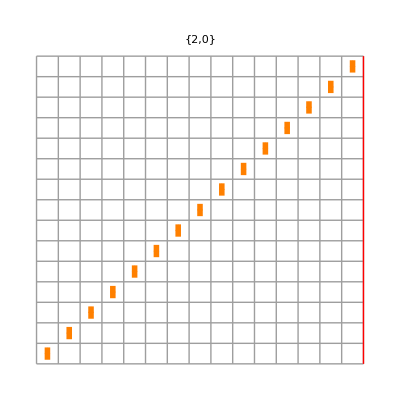
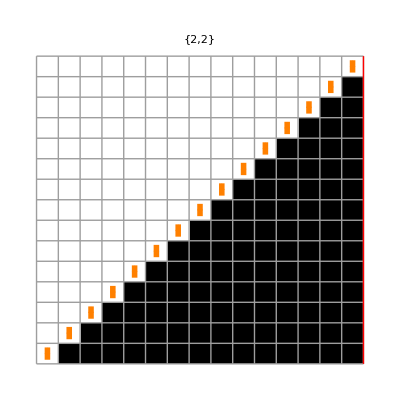
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SBTM[2,#,15]&/@{0,2,4,6,68,70,78,86,94,102,110,118,126,132,134,196,198,206,214,222,230,238,246,254,260,262,324,326,388,390,452,454,462,470,478,486,494,502,510,708,742,758,838,966,1220,1254,1270,1350,1478,1486,1494,1502,1510,1518,1526,1534,1732,1766,1782,1862,1990,2244,2278,2294,2374,2502,2756,2790,2806,2886,3014,3268,3276,3284,3292,3300,3302,3308,3316,3318,3324,3398,3526,3780,3814,3830,3910,4038}
```

```mathematica
SBTM[2,#,15]&/@{0,4}
```

{-Graphics-,-Graphics-}

```mathematica
nb=residu[[1]];result=Append[result,nb];
```

```mathematica
result
```

{0,2,4,6,68,70,78,86,94,102,110,118,126,132,134,196,198,206,214,222,230,238,246,254,260,262,324,326,388,390,452,454,462,470,478,486,494,502,510,708,742,758,838,966,1220,1254,1270,1350,1478,1486,1494,1502,1510,1518,1526,1534,1732,1766,1782,1862,1990,2244,2278,2294,2374,2502,2756,2790,2806,2886,3014,3268,3276,3284,3292,3300,3302,3308,3316,3318,3324,3398,3526,3780,3814,3830,3910,4038}

```mathematica
nb
```

4038

```mathematica
pos=Complement[Range[2S],Union[Base4SPositions[S,nb,50]]]
```

{3}

```mathematica
v=PadLeft[IntegerDigits[nb,4S ],2S ]
```

{7,7,0,6}

```mathematica
Union[Base4SPositions[S,nb,50]]
```

{1,2,4}

```mathematica
FromDigits[#,4  S]&/@     Partition[Flatten[Table[Evaluate@ReplacePart[v,Thread[pos->Table[ii[k],{k,Length[pos]}]]],Evaluate[Sequence@@Map[{#,0,4S-1}&,Table[ii[k],{k,Length[pos]}]]]]] ,2S]
```

{4038,4046,4054,4062,4070,4078,4086,4094}

```mathematica
FromDigits[#,4  S]&/@Flatten[Table[Evaluate@ReplacePart[v,Thread[pos->Table[ii[k],{k,Length[pos]}]]],Evaluate[Sequence@@Map[{#,0,4S-1}&,Table[ii[k],{k,Length[pos]}]]]]]
```

FromDigits::nlst: The expression 7 is not a list of digits or a string of valid digits.

FromDigits::nlst: The expression 0 is not a list of digits or a string of valid digits.

General::stop: Further output of FromDigits :: nlst will be suppressed during this calculation.

{FromDigits[7,8],FromDigits[7,8],FromDigits[0,8],FromDigits[6,8],FromDigits[7,8],FromDigits[7,8],FromDigits[1,8],FromDigits[6,8],FromDigits[7,8],FromDigits[7,8],FromDigits[2,8],FromDigits[6,8],FromDigits[7,8],FromDigits[7,8],FromDigits[3,8],FromDigits[6,8],FromDigits[7,8],FromDigits[7,8],FromDigits[4,8],FromDigits[6,8],FromDigits[7,8],FromDigits[7,8],FromDigits[5,8],FromDigits[6,8],FromDigits[7,8],FromDigits[7,8],FromDigits[6,8],FromDigits[6,8],FromDigits[7,8],FromDigits[7,8],FromDigits[7,8],FromDigits[6,8]}

```mathematica
residu=Complement[residu,FromDigits[#,4  S]&/@Flatten[Table[Evaluate@ReplacePart[v,Thread[pos->Table[ii[k],{k,Length[pos]}]]],Evaluate[Sequence@@Map[{#,0,4S-1}&,Table[ii[k],{k,Length[pos]}]]]],2]]
```

{2,4,6,10,12,14,18,20,22,26,28,30,34,36,38,42,44,46,50,52,54,58,60,62,66,68,70,74,76,78,82,84,86,90,92,94,98,100,102,106,108,110,114,116,118,122,124,126,130,132,134,138,140,142,146,148,150,154,156,158,162,164,166,170,172,174,178,180,182,186,188,190,194,196,198,202,204,206,210,212,214,218,220,222,226,228,230,234,236,238,242,244,246,250,252,254,258,260,262,266,268,270,274,276,278,282,284,286,290,292,294,298,300,302,306,308,310,314,316,318,322,324,326,330,332,334,338,340,342,346,348,350,354,356,358,362,364,366,370,372,374,378,380,382,386,388,390,394,396,398,402,404,406,410,412,414,418,420,422,426,428,430,434,436,438,442,444,446,450,452,454,458,460,462,466,468,470,474,476,478,482,484,486,490,492,494,498,500,502,506,508,510,514,516,518,522,524,526,530,532,534,538,540,542,546,548,550,554,556,558,562,564,566,570,572,574,578,580,582,586,588,590,594,596,598,602,604,606,610,612,614,618,620,622,626,628,630,634,636,638,642,644,646,650,652,654,658,660,662,666,668,670,674,676,678,682,684,686,690,692,694,698,700,702,706,708,710,714,716,718,722,724,726,730,732,734,738,740,742,746,748,750,754,756,758,762,764,766,770,772,774,778,780,782,786,788,790,794,796,798,802,804,806,810,812,814,818,820,822,826,828,830,834,836,838,842,844,846,850,852,854,858,860,862,866,868,870,874,876,878,882,884,886,890,892,894,898,900,902,906,908,910,914,916,918,922,924,926,930,932,934,938,940,942,946,948,950,954,956,958,962,964,966,970,972,974,978,980,982,986,988,990,994,996,998,1002,1004,1006,1010,1012,1014,1018,1020,1022,1026,1028,1030,1034,1036,1038,1042,1044,1046,1050,1052,1054,1058,1060,1062,1066,1068,1070,1074,1076,1078,1082,1084,1086,1090,1092,1094,1098,1100,1102,1106,1108,1110,1114,1116,1118,1122,1124,1126,1130,1132,1134,1138,1140,1142,1146,1148,1150,1154,1156,1158,1162,1164,1166,1170,1172,1174,1178,1180,1182,1186,1188,1190,1194,1196,1198,1202,1204,1206,1210,1212,1214,1218,1220,1222,1226,1228,1230,1234,1236,1238,1242,1244,1246,1250,1252,1254,1258,1260,1262,1266,1268,1270,1274,1276,1278,1282,1284,1286,1290,1292,1294,1298,1300,1302,1306,1308,1310,1314,1316,1318,1322,1324,1326,1330,1332,1334,1338,1340,1342,1346,1348,1350,1354,1356,1358,1362,1364,1366,1370,1372,1374,1378,1380,1382,1386,1388,1390,1394,1396,1398,1402,1404,1406,1410,1412,1414,1418,1420,1422,1426,1428,1430,1434,1436,1438,1442,1444,1446,1450,1452,1454,1458,1460,1462,1466,1468,1470,1474,1476,1478,1482,1484,1486,1490,1492,1494,1498,1500,1502,1506,1508,1510,1514,1516,1518,1522,1524,1526,1530,1532,1534,1538,1540,1542,1546,1548,1550,1554,1556,1558,1562,1564,1566,1570,1572,1574,1578,1580,1582,1586,1588,1590,1594,1596,1598,1602,1604,1606,1610,1612,1614,1618,1620,1622,1626,1628,1630,1634,1636,1638,1642,1644,1646,1650,1652,1654,1658,1660,1662,1666,1668,1670,1674,1676,1678,1682,1684,1686,1690,1692,1694,1698,1700,1702,1706,1708,1710,1714,1716,1718,1722,1724,1726,1730,1732,1734,1738,1740,1742,1746,1748,1750,1754,1756,1758,1762,1764,1766,1770,1772,1774,1778,1780,1782,1786,1788,1790,1794,1796,1798,1802,1804,1806,1810,1812,1814,1818,1820,1822,1826,1828,1830,1834,1836,1838,1842,1844,1846,1850,1852,1854,1858,1860,1862,1866,1868,1870,1874,1876,1878,1882,1884,1886,1890,1892,1894,1898,1900,1902,1906,1908,1910,1914,1916,1918,1922,1924,1926,1930,1932,1934,1938,1940,1942,1946,1948,1950,1954,1956,1958,1962,1964,1966,1970,1972,1974,1978,1980,1982,1986,1988,1990,1994,1996,1998,2002,2004,2006,2010,2012,2014,2018,2020,2022,2026,2028,2030,2034,2036,2038,2042,2044,2046,2050,2052,2054,2058,2060,2062,2066,2068,2070,2074,2076,2078,2082,2084,2086,2090,2092,2094,2098,2100,2102,2106,2108,2110,2114,2116,2118,2122,2124,2126,2130,2132,2134,2138,2140,2142,2146,2148,2150,2154,2156,2158,2162,2164,2166,2170,2172,2174,2178,2180,2182,2186,2188,2190,2194,2196,2198,2202,2204,2206,2210,2212,2214,2218,2220,2222,2226,2228,2230,2234,2236,2238,2242,2244,2246,2250,2252,2254,2258,2260,2262,2266,2268,2270,2274,2276,2278,2282,2284,2286,2290,2292,2294,2298,2300,2302,2306,2308,2310,2314,2316,2318,2322,2324,2326,2330,2332,2334,2338,2340,2342,2346,2348,2350,2354,2356,2358,2362,2364,2366,2370,2372,2374,2378,2380,2382,2386,2388,2390,2394,2396,2398,2402,2404,2406,2410,2412,2414,2418,2420,2422,2426,2428,2430,2434,2436,2438,2442,2444,2446,2450,2452,2454,2458,2460,2462,2466,2468,2470,2474,2476,2478,2482,2484,2486,2490,2492,2494,2498,2500,2502,2506,2508,2510,2514,2516,2518,2522,2524,2526,2530,2532,2534,2538,2540,2542,2546,2548,2550,2554,2556,2558,2562,2564,2566,2570,2572,2574,2578,2580,2582,2586,2588,2590,2594,2596,2598,2602,2604,2606,2610,2612,2614,2618,2620,2622,2626,2628,2630,2634,2636,2638,2642,2644,2646,2650,2652,2654,2658,2660,2662,2666,2668,2670,2674,2676,2678,2682,2684,2686,2690,2692,2694,2698,2700,2702,2706,2708,2710,2714,2716,2718,2722,2724,2726,2730,2732,2734,2738,2740,2742,2746,2748,2750,2754,2756,2758,2762,2764,2766,2770,2772,2774,2778,2780,2782,2786,2788,2790,2794,2796,2798,2802,2804,2806,2810,2812,2814,2818,2820,2822,2826,2828,2830,2834,2836,2838,2842,2844,2846,2850,2852,2854,2858,2860,2862,2866,2868,2870,2874,2876,2878,2882,2884,2886,2890,2892,2894,2898,2900,2902,2906,2908,2910,2914,2916,2918,2922,2924,2926,2930,2932,2934,2938,2940,2942,2946,2948,2950,2954,2956,2958,2962,2964,2966,2970,2972,2974,2978,2980,2982,2986,2988,2990,2994,2996,2998,3002,3004,3006,3010,3012,3014,3018,3020,3022,3026,3028,3030,3034,3036,3038,3042,3044,3046,3050,3052,3054,3058,3060,3062,3066,3068,3070,3074,3076,3078,3082,3084,3086,3090,3092,3094,3098,3100,3102,3106,3108,3110,3114,3116,3118,3122,3124,3126,3130,3132,3134,3138,3140,3142,3146,3148,3150,3154,3156,3158,3162,3164,3166,3170,3172,3174,3178,3180,3182,3186,3188,3190,3194,3196,3198,3202,3204,3206,3210,3212,3214,3218,3220,3222,3226,3228,3230,3234,3236,3238,3242,3244,3246,3250,3252,3254,3258,3260,3262,3266,3268,3270,3274,3276,3278,3282,3284,3286,3290,3292,3294,3298,3300,3302,3306,3308,3310,3314,3316,3318,3322,3324,3326,3330,3332,3334,3338,3340,3342,3346,3348,3350,3354,3356,3358,3362,3364,3366,3370,3372,3374,3378,3380,3382,3386,3388,3390,3394,3396,3398,3402,3404,3406,3410,3412,3414,3418,3420,3422,3426,3428,3430,3434,3436,3438,3442,3444,3446,3450,3452,3454,3458,3460,3462,3466,3468,3470,3474,3476,3478,3482,3484,3486,3490,3492,3494,3498,3500,3502,3506,3508,3510,3514,3516,3518,3522,3524,3526,3530,3532,3534,3538,3540,3542,3546,3548,3550,3554,3556,3558,3562,3564,3566,3570,3572,3574,3578,3580,3582,3586,3588,3590,3594,3596,3598,3602,3604,3606,3610,3612,3614,3618,3620,3622,3626,3628,3630,3634,3636,3638,3642,3644,3646,3650,3652,3654,3658,3660,3662,3666,3668,3670,3674,3676,3678,3682,3684,3686,3690,3692,3694,3698,3700,3702,3706,3708,3710,3714,3716,3718,3722,3724,3726,3730,3732,3734,3738,3740,3742,3746,3748,3750,3754,3756,3758,3762,3764,3766,3770,3772,3774,3778,3780,3782,3786,3788,3790,3794,3796,3798,3802,3804,3806,3810,3812,3814,3818,3820,3822,3826,3828,3830,3834,3836,3838,3842,3844,3846,3850,3852,3854,3858,3860,3862,3866,3868,3870,3874,3876,3878,3882,3884,3886,3890,3892,3894,3898,3900,3902,3906,3908,3910,3914,3916,3918,3922,3924,3926,3930,3932,3934,3938,3940,3942,3946,3948,3950,3954,3956,3958,3962,3964,3966,3970,3972,3974,3978,3980,3982,3986,3988,3990,3994,3996,3998,4002,4004,4006,4010,4012,4014,4018,4020,4022,4026,4028,4030,4034,4036,4038,4042,4044,4046,4050,4052,4054,4058,4060,4062,4066,4068,4070,4074,4076,4078,4082,4084,4086,4090,4092,4094}

```mathematica
nb=residu[[1]];result=Append[result,nb];
```

```mathematica
result
```

{0,2}

```mathematica
pos=Complement[Range[2S],Union[Base4SPositions[S,nb,50]]]
```

{1,2,3}

```mathematica
v=PadLeft[IntegerDigits[nb,4S ],2S ]
```

{0,0,0,2}

```mathematica
residu=Complement[residu,FromDigits[#,4  S]&/@Flatten[Table[Evaluate@ReplacePart[v,Thread[pos->Table[ii[k],{k,Length[pos]}]]],Evaluate[Sequence@@Map[{#,0,4S-1}&,Table[ii[k],{k,Length[pos]}]]]],2]]
```

{4,6,12,14,20,22,28,30,36,38,44,46,52,54,60,62,68,70,76,78,84,86,92,94,100,102,108,110,116,118,124,126,132,134,140,142,148,150,156,158,164,166,172,174,180,182,188,190,196,198,204,206,212,214,220,222,228,230,236,238,244,246,252,254,260,262,268,270,276,278,284,286,292,294,300,302,308,310,316,318,324,326,332,334,340,342,348,350,356,358,364,366,372,374,380,382,388,390,396,398,404,406,412,414,420,422,428,430,436,438,444,446,452,454,460,462,468,470,476,478,484,486,492,494,500,502,508,510,516,518,524,526,532,534,540,542,548,550,556,558,564,566,572,574,580,582,588,590,596,598,604,606,612,614,620,622,628,630,636,638,644,646,652,654,660,662,668,670,676,678,684,686,692,694,700,702,708,710,716,718,724,726,732,734,740,742,748,750,756,758,764,766,772,774,780,782,788,790,796,798,804,806,812,814,820,822,828,830,836,838,844,846,852,854,860,862,868,870,876,878,884,886,892,894,900,902,908,910,916,918,924,926,932,934,940,942,948,950,956,958,964,966,972,974,980,982,988,990,996,998,1004,1006,1012,1014,1020,1022,1028,1030,1036,1038,1044,1046,1052,1054,1060,1062,1068,1070,1076,1078,1084,1086,1092,1094,1100,1102,1108,1110,1116,1118,1124,1126,1132,1134,1140,1142,1148,1150,1156,1158,1164,1166,1172,1174,1180,1182,1188,1190,1196,1198,1204,1206,1212,1214,1220,1222,1228,1230,1236,1238,1244,1246,1252,1254,1260,1262,1268,1270,1276,1278,1284,1286,1292,1294,1300,1302,1308,1310,1316,1318,1324,1326,1332,1334,1340,1342,1348,1350,1356,1358,1364,1366,1372,1374,1380,1382,1388,1390,1396,1398,1404,1406,1412,1414,1420,1422,1428,1430,1436,1438,1444,1446,1452,1454,1460,1462,1468,1470,1476,1478,1484,1486,1492,1494,1500,1502,1508,1510,1516,1518,1524,1526,1532,1534,1540,1542,1548,1550,1556,1558,1564,1566,1572,1574,1580,1582,1588,1590,1596,1598,1604,1606,1612,1614,1620,1622,1628,1630,1636,1638,1644,1646,1652,1654,1660,1662,1668,1670,1676,1678,1684,1686,1692,1694,1700,1702,1708,1710,1716,1718,1724,1726,1732,1734,1740,1742,1748,1750,1756,1758,1764,1766,1772,1774,1780,1782,1788,1790,1796,1798,1804,1806,1812,1814,1820,1822,1828,1830,1836,1838,1844,1846,1852,1854,1860,1862,1868,1870,1876,1878,1884,1886,1892,1894,1900,1902,1908,1910,1916,1918,1924,1926,1932,1934,1940,1942,1948,1950,1956,1958,1964,1966,1972,1974,1980,1982,1988,1990,1996,1998,2004,2006,2012,2014,2020,2022,2028,2030,2036,2038,2044,2046,2052,2054,2060,2062,2068,2070,2076,2078,2084,2086,2092,2094,2100,2102,2108,2110,2116,2118,2124,2126,2132,2134,2140,2142,2148,2150,2156,2158,2164,2166,2172,2174,2180,2182,2188,2190,2196,2198,2204,2206,2212,2214,2220,2222,2228,2230,2236,2238,2244,2246,2252,2254,2260,2262,2268,2270,2276,2278,2284,2286,2292,2294,2300,2302,2308,2310,2316,2318,2324,2326,2332,2334,2340,2342,2348,2350,2356,2358,2364,2366,2372,2374,2380,2382,2388,2390,2396,2398,2404,2406,2412,2414,2420,2422,2428,2430,2436,2438,2444,2446,2452,2454,2460,2462,2468,2470,2476,2478,2484,2486,2492,2494,2500,2502,2508,2510,2516,2518,2524,2526,2532,2534,2540,2542,2548,2550,2556,2558,2564,2566,2572,2574,2580,2582,2588,2590,2596,2598,2604,2606,2612,2614,2620,2622,2628,2630,2636,2638,2644,2646,2652,2654,2660,2662,2668,2670,2676,2678,2684,2686,2692,2694,2700,2702,2708,2710,2716,2718,2724,2726,2732,2734,2740,2742,2748,2750,2756,2758,2764,2766,2772,2774,2780,2782,2788,2790,2796,2798,2804,2806,2812,2814,2820,2822,2828,2830,2836,2838,2844,2846,2852,2854,2860,2862,2868,2870,2876,2878,2884,2886,2892,2894,2900,2902,2908,2910,2916,2918,2924,2926,2932,2934,2940,2942,2948,2950,2956,2958,2964,2966,2972,2974,2980,2982,2988,2990,2996,2998,3004,3006,3012,3014,3020,3022,3028,3030,3036,3038,3044,3046,3052,3054,3060,3062,3068,3070,3076,3078,3084,3086,3092,3094,3100,3102,3108,3110,3116,3118,3124,3126,3132,3134,3140,3142,3148,3150,3156,3158,3164,3166,3172,3174,3180,3182,3188,3190,3196,3198,3204,3206,3212,3214,3220,3222,3228,3230,3236,3238,3244,3246,3252,3254,3260,3262,3268,3270,3276,3278,3284,3286,3292,3294,3300,3302,3308,3310,3316,3318,3324,3326,3332,3334,3340,3342,3348,3350,3356,3358,3364,3366,3372,3374,3380,3382,3388,3390,3396,3398,3404,3406,3412,3414,3420,3422,3428,3430,3436,3438,3444,3446,3452,3454,3460,3462,3468,3470,3476,3478,3484,3486,3492,3494,3500,3502,3508,3510,3516,3518,3524,3526,3532,3534,3540,3542,3548,3550,3556,3558,3564,3566,3572,3574,3580,3582,3588,3590,3596,3598,3604,3606,3612,3614,3620,3622,3628,3630,3636,3638,3644,3646,3652,3654,3660,3662,3668,3670,3676,3678,3684,3686,3692,3694,3700,3702,3708,3710,3716,3718,3724,3726,3732,3734,3740,3742,3748,3750,3756,3758,3764,3766,3772,3774,3780,3782,3788,3790,3796,3798,3804,3806,3812,3814,3820,3822,3828,3830,3836,3838,3844,3846,3852,3854,3860,3862,3868,3870,3876,3878,3884,3886,3892,3894,3900,3902,3908,3910,3916,3918,3924,3926,3932,3934,3940,3942,3948,3950,3956,3958,3964,3966,3972,3974,3980,3982,3988,3990,3996,3998,4004,4006,4012,4014,4020,4022,4028,4030,4036,4038,4044,4046,4052,4054,4060,4062,4068,4070,4076,4078,4084,4086,4092,4094}